```mathematica
Needs["GraphUtilities`"]
Needs["PlotLegends`"]
(* Read Cell/Pos/Cont Data Files *)
CellFile[i_]:="cell_"<>ToString[i];
PosFile[i_]:="pos_"<>ToString[i];
ContFile[i_]:="cont_"<>ToString[i];
C0=0.000001;
ReadFile[File_,Cn_,Data_]:={
stream=OpenRead[File];
Col=Table["Number",{i,1,Cn}];
Data=ReadList[stream,Col];
Close[stream];}
PlotOption={ViewPoint->{0,0,1000},Boxed->False,PlotRange->{{-6,6},{-25.5,25.5},{-5.5,5.5}},Lighting->{{"Directional",White,{20,10,100}},{"Directional",White,{-20,-10,-100}}},ImageSize->100};Color=0.66;
Par[n_]:={
Clear[Particles];Clear[Contacts];
ReadFile[PosFile[n],14,Particles];
text=ToString[n];
Graphics3D[{Table[{Hue[Color (Particles[[i,14]]/(Particles[[i,14]]/Particles[[i,13]]+4/3π Particles[[i,10]]^3))],Sphere[{Particles[[i,1]],Particles[[i,2]],Particles[[i,3]]},Particles[[i,10]]]},{i,1,Dimensions[Particles][[1]]}]},PlotOption]
};
ParV[n_]:={
Clear[Particles];Clear[Contacts];
ReadFile[PosFile[n],14,Particles];
text=ToString[n];
Graphics3D[{Table[{Hue[Color (Norm[{Particles[[i+1,4]],Particles[[i+1,5]],Particles[[i+1,6]]}])],Sphere[{Particles[[i+1,1]],Particles[[i+1,2]],Particles[[i+1,3]]},Particles[[i+1,10]]]},{i,0,Dimensions[Particles][[1]]-1}]},PlotOption]
(*ListVectorPlot3D[Table[{{Particles[[i+1,1]],Particles[[i+1,2]],Particles[[i+1,3]]},{Particles[[i+1,4]],Particles[[i+1,5]],Particles[[i+1,6]]}},{i,0,Dimensions[Particles][[1]]-1}],PlotOption]*)
};
G[n_]:={
Clear[Particles];Clear[Contacts];
ReadFile[PosFile[n],14,Particles];
ReadFile[ContFile[n],16,Contacts];
Num=Dimensions[Contacts][[1]];NP=Dimensions[Particles][[1]];
P={};nend=FileNames[{"pos*"}]//Length;
text=ToString[n];
For[i=1,i<NP,i++,{Particles[[i,13]]=0}]
For[i=1,i<Num+1,i++,
If[Contacts[[i,16]]>0.0,
{P=Append[P,Contacts[[i,1]]],P=Append[P,Contacts[[i,2]]],Particles[[Contacts[[i,1]]+1,13]]=Particles[[Contacts[[i,1]]+1,13]]+1,
Particles[[Contacts[[i,2]]+1,13]]=Particles[[Contacts[[i,2]]+1,13]]+1}
]];
P=DeleteDuplicates[P];
Graphics3D[Table[{Hue[Color(Particles[[P[[i]]+1,13]]/6)],Sphere[{Particles[[P[[i]]+1,1]],Particles[[P[[i]]+1,2]],Particles[[P[[i]]+1,3]]},Particles[[P[[i]]+1,10]]]},{i,1,Dimensions[P][[1]]}],PlotOption]
};
ContactChange[n_,n0_]:={
Clear[Particles];Clear[Contacts];Clear[Particles0];Clear[Contacts0];
If[n≤n0,n0=n-1];
ReadFile[PosFile[n0],14,Particles0];
ReadFile[ContFile[n0],16,Contacts0];
Num=Dimensions[Contacts0][[1]];NP=Dimensions[Particles0][[1]];
For[i=1,i<NP,i++,{Particles0[[i,13]]=0}];
For[i=1,i<Num+1,i++,
If[Contacts0[[i,16]]>0.0,
{Particles0[[Contacts0[[i,1]]+1,13]]=Particles0[[Contacts0[[i,1]]+1,13]]+1,
Particles0[[Contacts0[[i,2]]+1,13]]=Particles0[[Contacts0[[i,2]]+1,13]]+1}
]];

ReadFile[PosFile[n],14,Particles];
ReadFile[ContFile[n],16,Contacts];
Num=Dimensions[Contacts][[1]];NP=Dimensions[Particles][[1]];
text=ToString[n];
For[i=1,i<NP,i++,{Particles[[i,13]]=0}]
For[i=1,i<Num+1,i++,
If[Contacts[[i,16]]>0.0,
{Particles[[Contacts[[i,1]]+1,13]]=Particles[[Contacts[[i,1]]+1,13]]+1,
Particles[[Contacts[[i,2]]+1,13]]=Particles[[Contacts[[i,2]]+1,13]]+1}
]];
For[i=1,i<NP,i++,
{Particles[[i,13]]=(1-(Particles0[[i,13]]-Particles[[i,13]])/(Particles0[[i,13]]+1))}];

Graphics3D[Table[{Hue[Color(Particles[[i,13]])],Sphere[{Particles[[i,1]],Particles[[i,2]],Particles[[i,3]]},Particles[[i,10]]]},{i,1,Dimensions[Particles][[1]]}],PlotOption]
};


WaterRentantion[n_]:={
Clear[Particles];
ReadFile[PosFile[n],14,Particles];
ListPlot[Table[{Particles[[i,13]],-100.0*Particles[[i,12]]},{i,1,Dimensions[Particles][[1]]}],Frame->True,FrameLabel->{"Degree of Saturation","Water Pressure"}]
};
ExportPlots[i_]:={
Export["~/Profile"<>ToString[i]<>".png",Par[i][[1]]];
Export["~/Pressure"<>ToString[i]<>".pdf",WaterRentantion[i][[1]]];}
```

500

210

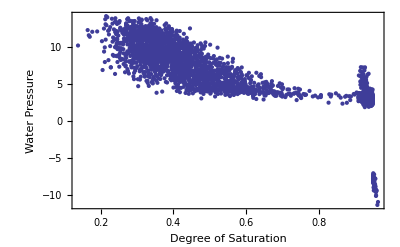

500

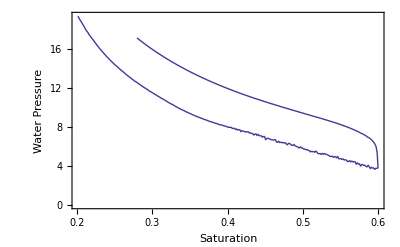

```mathematica
SetDirectory["/home/yixiang/Desktop/DEM_2012_Capillary/data/g1e-3_s0206"];
ii=FileNames[{"pos*"}]//Length
ii=210
PW=WaterRentantion[ii][[1]]

Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True]
```

```mathematica
ii=250
PP={Show[Par[ii]],Show[Par[ii-10]],Show[Par[ii-20]],Show[Par[ii-50]]}
```

250

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

456

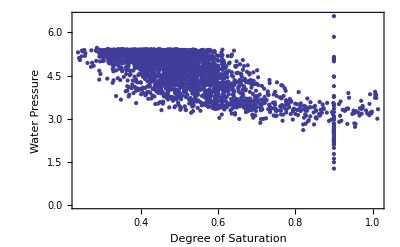

{-Graphics3D-,-Graphics3D-}

```mathematica
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning01/data/g2e-3_s0208"];
ii=FileNames[{"pos*"}]//Length
PW=WaterRentantion[ii][[1]]
PP={Show[Par[ii]],Show[Par[ii-20]]}
SetDirectory["/home/yixiang/"];
(*Export["g1e-4_d.png",PW]
Export["g1e-4_s.png",PP]
*)
```

500

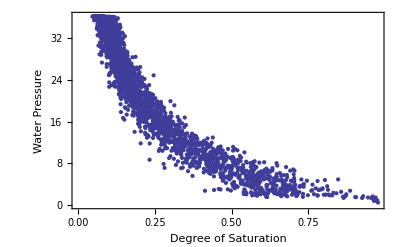

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

495

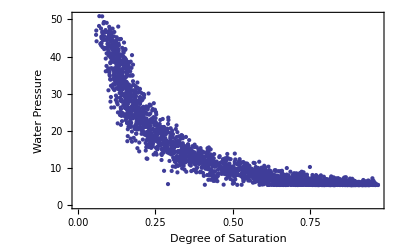

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning10/data/g1e-3_s0208"];
ii=FileNames[{"pos*"}]//Length
PW=WaterRentantion[ii][[1]]
PP={Show[Par[ii]],Show[Par[ii-100]],Show[Par[ii-200]],Show[Par[ii-300]],Show[Par[ii-400]]}
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning10/data/g1e-8_s0208"];
ii=FileNames[{"pos*"}]//Length
PW=WaterRentantion[ii][[1]]
PP={Show[Par[ii]],Show[Par[ii-100]],Show[Par[ii-200]],Show[Par[ii-300]],Show[Par[ii-400]]}
(*Export["g1e-4_d.png",PW]
Export["g1e-4_s.png",PP]
```

498

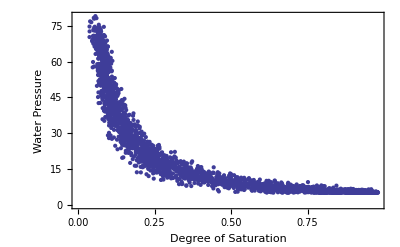

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning10/data/g1e-8_s0406"];
ii=FileNames[{"pos*"}]//Length
PW=WaterRentantion[ii][[1]]
PP={Show[Par[ii]],Show[Par[ii-100]],Show[Par[ii-200]],Show[Par[ii-300]],Show[Par[ii-400]]}
(*Export["g1e-4_d.png",PW]
Export["g1e-4_s.png",PP]
```

19

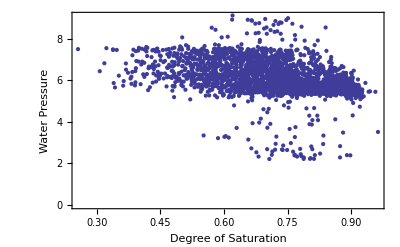

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

17

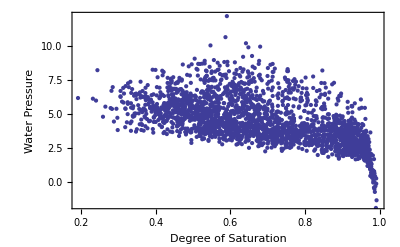

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning13/data/g1e-8_s0208"];
ii=FileNames[{"pos*"}]//Length
PW=WaterRentantion[ii][[1]]
PP={Show[Par[ii]],Show[Par[ii-1]],Show[Par[ii-2]],Show[Par[ii-3]],Show[Par[ii-4]]}
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning13/data/g1e-3_s0208"];
ii=FileNames[{"pos*"}]//Length
PW=WaterRentantion[ii][[1]]
PP={Show[Par[ii]],Show[Par[ii-1]],Show[Par[ii-2]],Show[Par[ii-3]],Show[Par[ii-4]]}
(*Export["g1e-4_d.png",PW]
Export["g1e-4_s.png",PP]
```

12

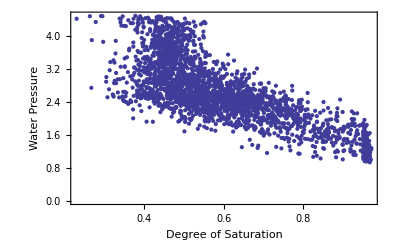

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning17/data/g2e-3_s0208"];
ii=FileNames[{"pos*"}]//Length
PW=WaterRentantion[ii][[1]]
PP={Show[Par[ii]],Show[Par[ii-1]],Show[Par[ii-2]],Show[Par[ii-3]],Show[Par[ii-4]]}
```

2000

2000

2000

«1 more identical outputs»

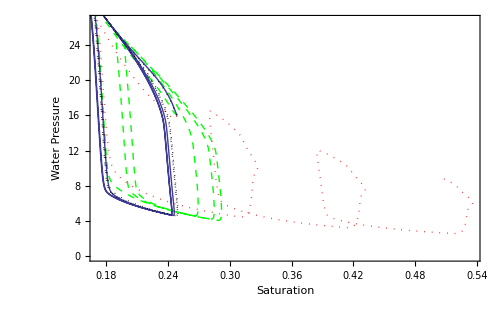

```mathematica
Clear[Data30]
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning/data/sigma1e-2_scanning"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P1=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500];
Clear[Data30]
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning/data/sigma1e-2_scanning_5e-3"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P2=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Green}];
Clear[Data30]
SetDirectory["/home/yixiang/Desktop/DEM_2012_Capillary/data/sigma1e-2_scanning2"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P3=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
SetDirectory["/home/yixiang/Desktop/DEM_2012_Capillary/data/sigma1e-2_scanning3"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P4=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Black}];
Show[{P3,P2,P1,P4}]
```

1819

1821

1818

1885

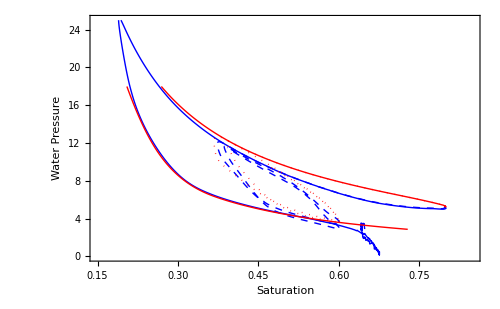

```mathematica
Clear[Data30]
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning/data/g5e-3_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P1=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Blue},PlotRange->{{0.15,0.85},{0,25}}];
Clear[Data30]
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning/data/g5e-3_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P2=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Blue}];
Clear[Data30]
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning/data/g5e-4_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P3=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Red}];
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning/data/g5e-4_s0406"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P4=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
Show[{P1,P2,P3,P4}]
```

5000

2000

5000

5000

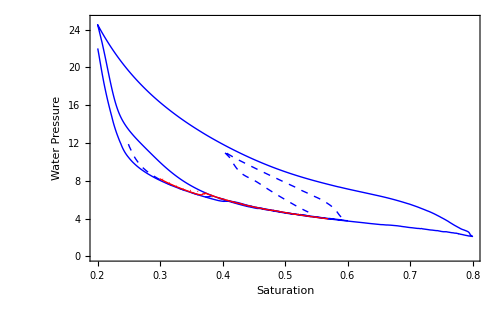

```mathematica
(*wetting from top*)
Clear[Data30]
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning01/data/g2e-3_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P1=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Blue},PlotRange->{{0.2,0.8},{0,25}}];
Clear[Data30]
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning01/data/g2e-3_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P2=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Blue}];
Clear[Data30]
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning01/data/g1e-4_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P3=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Red}];
SetDirectory["/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning01/data/g1e-4_s0406"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P4=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
Show[{P1,P2,P3,P4}]
```

5000

5000

5000

«3 more identical outputs»

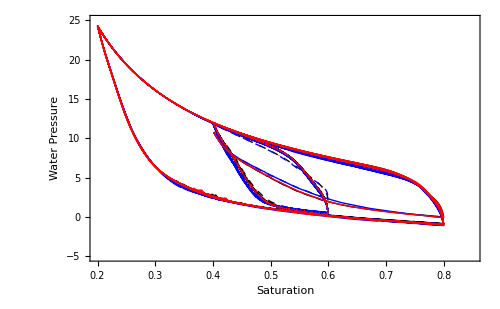

```mathematica
(* pressure control for water tranport, stress control, dwater rate *)
Clear[Data30]
folder="/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning10/data/";
SetDirectory[folder<>"g1e-8_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P1=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Black},PlotRange->{{0.2,0.85},{-5,25}}];
Clear[Data30]
SetDirectory[folder<>"g1e-8_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P2=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Black}];
Clear[Data30]
SetDirectory[folder<>"g1e-3_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P3=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Blue}];
Clear[Data30]
SetDirectory[folder<>"g1e-3_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P4=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Blue}];
Clear[Data30]
SetDirectory[folder<>"g1e-4_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P5=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Red}];
SetDirectory[folder<>"g1e-4_s0406"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P6=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
Show[{P1,P2,P3,P4,P5,P6}]
```

2771

2655

1440

1502

2598

2635

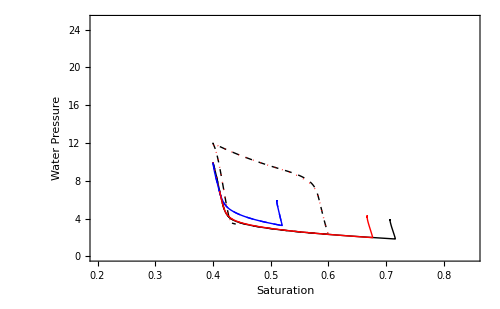

```mathematica
(* pressure control for water tranport, stress control, dwater rate *)
Clear[Data30]
folder="/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning12/data/";
SetDirectory[folder<>"g1e-8_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P1=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Black},PlotRange->{{0.2,0.85},{0,25}}];
Clear[Data30]
SetDirectory[folder<>"g1e-8_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P2=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Black}];
Clear[Data30]
SetDirectory[folder<>"g1e-3_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P3=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Blue}];
Clear[Data30]
SetDirectory[folder<>"g1e-3_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P4=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Blue}];
Clear[Data30]
SetDirectory[folder<>"g1e-4_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P5=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Red}];
SetDirectory[folder<>"g1e-4_s0406"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P6=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
Show[{P1,P2,P3,P4,P5,P6}]
```

1147

1109

148

1023

1114

1051

143

81

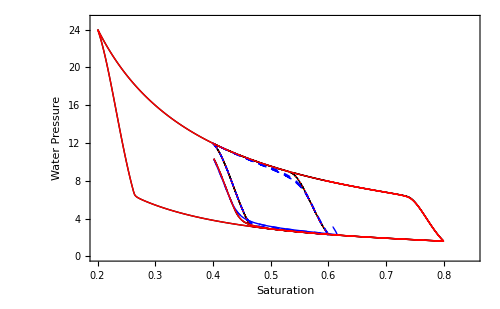

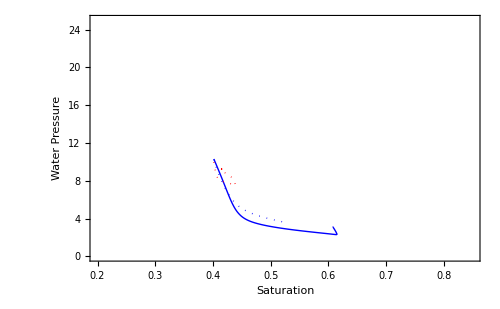

```mathematica
(* pressure control for water tranport, stress control, dwater rate *)
Clear[Data30]
folder="/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning15/data/";
SetDirectory[folder<>"g1e-8_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P1=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Black},PlotRange->{{0.2,0.85},{0,25}}];
Clear[Data30]
SetDirectory[folder<>"g1e-8_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P2=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Black}];
Clear[Data30]
SetDirectory[folder<>"g1e-3_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P3=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Blue},PlotRange->{{0.2,0.85},{0,25}}];
Clear[Data30]
SetDirectory[folder<>"g1e-3_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P4=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Blue}];
Clear[Data30]
SetDirectory[folder<>"g1e-4_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P5=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Red}];
SetDirectory[folder<>"g1e-4_s0406"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P6=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
SetDirectory[folder<>"g5e-3_s0208"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P7=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
SetDirectory[folder<>"g2e-3_s0208"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P8=ListPlot[{Table[{Data30[[i,7]],Data30[[i,8]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Blue}];
Show[{P1,P2,P3,P4,P5,P6}]
Show[{P3,P7,P8}]
```

1359

1417

1419

1357

1262

1418

2693

1359

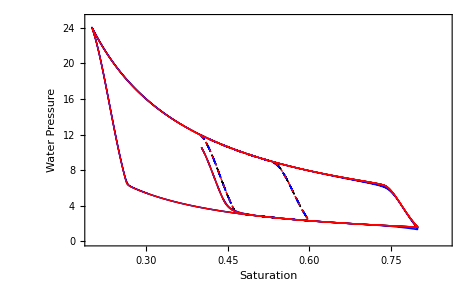

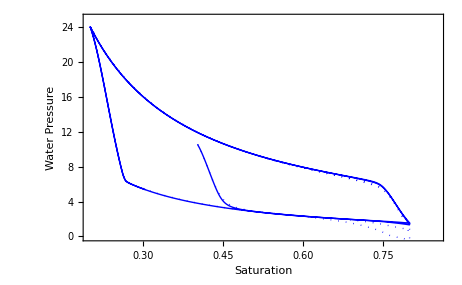

```mathematica
(* pressure control for water tranport, stress control, homogenised water wetting *)
Clear[Data30]
folder="/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning16/data/";
SetDirectory[folder<>"g1e-8_s0208"];ploti=8;
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P1=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Black},PlotRange->{{0.2,0.85},{0,25}}];
Clear[Data30]
SetDirectory[folder<>"g1e-8_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P2=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Black}];
Clear[Data30]
SetDirectory[folder<>"g1e-3_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P3=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Blue},PlotRange->{{0.2,0.85},{0,25}}];
Clear[Data30]
SetDirectory[folder<>"g1e-3_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P4=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Blue}];
Clear[Data30]
SetDirectory[folder<>"g1e-4_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P5=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Red}];
SetDirectory[folder<>"g1e-4_s0406"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P6=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
SetDirectory[folder<>"g5e-3_s0208"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P7=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
SetDirectory[folder<>"g2e-3_s0208"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P8=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Blue}];
Show[{P1,P2,P3,P4,P5,P6}]
Show[{P3,P8}]
```

2773

2769

2770

2765

2749

2754

2715

2618

2697

2578

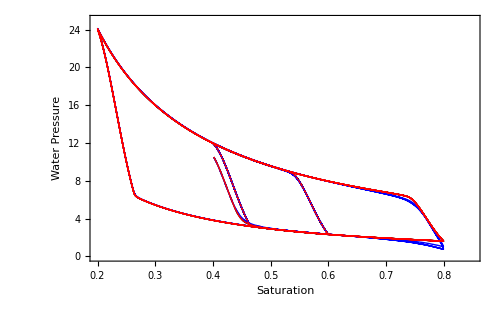

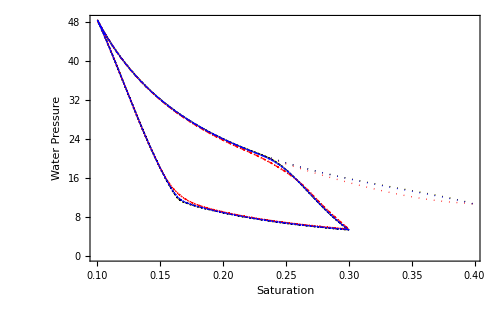

```mathematica
(* pressure control for water tranport, stress control, homogenised water wetting *)
Clear[Data30]
folder="/home/yixiang/.gvfs/sftp for yixiang on 129.78.142.233/home/yixiang/work/DEM_2012_Capillary_Scanning17/data/";
SetDirectory[folder<>"g1e-8_s0208"];ploti=8;
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P1=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Black},PlotRange->{{0.2,0.85},{0,25}}];
Clear[Data30]
SetDirectory[folder<>"g1e-8_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P2=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Black}];
Clear[Data30]
SetDirectory[folder<>"g1e-3_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P3=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Blue},PlotRange->{{0.2,0.85},{0,25}}];
Clear[Data30]
SetDirectory[folder<>"g1e-3_s0406"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P4=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dashed,Thick,Blue}];
Clear[Data30]
SetDirectory[folder<>"g1e-4_s0208"];
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P5=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Thick,Red}];
SetDirectory[folder<>"g1e-4_s0406"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P6=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
SetDirectory[folder<>"g5e-3_s0103"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P7=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Red}];
SetDirectory[folder<>"g2e-3_s0103"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P8=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Blue}];
SetDirectory[folder<>"g1e-3_s0103"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P9=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Black}];
SetDirectory[folder<>"g1e-4_s0103"];
Clear[Data30]
ReadFile["ahistory",9,Data30];Dimensions[Data30][[1]]
P10=ListPlot[{Table[{Data30[[i,7]],Data30[[i,ploti]]},{i,2,Dimensions[Data30][[1]]}]},Frame->True,FrameLabel->{"Saturation","Water Pressure"},Joined->True,ImageSize->500,PlotStyle->{Dotted,Thick,Yellow}];
Show[{P1,P2,P3,P4,P5,P6}]
Show[{P10,P9,P7,P8}]
```

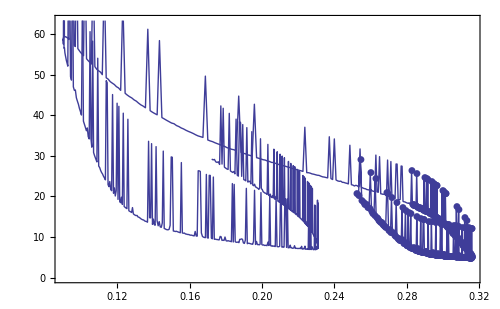

```mathematica
(*"/home/yixiang/Desktop/DEM_2012_Capillary/data/sigma1e-2_scanning2"*)
```